# HW #4: 4.1 # 1, 2, 3, 4, 9, 11, 15, 19, 23, 31, 32

## Cole Pendergraft

## 4.1 # 1

Use the Lagrange interpolation process to obtain a polynomial of least degree that assumes these values:

						x | 0 | 2 | 3 | 4
y | 7 | 11 | 28 | 63

The Lagrange method tells us that l_i (x) =  (Π^n)_(j = 0
j≠ i) (x - x_j)/(x_i - x_j), and further that P_n(x) = (Σ^n)_(i = 0) l_i (x)f(x_i). So we can start by establishing l_0 to l_3.

```mathematica
Clear[l0];
l0[x_] = ((x-2)(x-3)(x-4))/(-24);

Clear[l1];
l1[x_] = ((x)(x-3)(x-4)) / (4) ;

Clear[l2];
l2[x_] = ((x)(x-2)(x-4))/(-3);

Clear[l3];
l3[x_] = ((x)(x-2)(x-3))/(8);

Clear[p];
(* Now all we have to do is add all the l functions into the format for P_n as shown above *)
Simplify[p[x_] = 7l0[x] + 11l1[x] + 28l2[x] + 63l3[x]]
```

7-2 x+x^3

```mathematica
p[0]
p[2]
p[3]
p[4]
```

7

11

28

63

## 4.1 # 2

(Continuation) Rearrange the points in the table of the preceding problem and find the Newton form of the interpolating polynomial. Show that the polynomials obtained are identical, although their forms may differ.

																	Rearranged table:	 x | 4 | 3 | 2 | 0
y | 63 | 28 | 11 | 7

```mathematica
Clear[p1];
(* Newton's method tells us that p1(x) = y_0 + c(x - x_0) *)
p1[x_] = 63 + c(x - 4);
(* Now we solve for c using the knowledge that p1[3] = 28. 28 = 63 + c(3 - 4) -> 28 = 63 - c -> c = 35. Now we can update p1 *)

Clear[p1];
p1[x_] = 63 + 35(x - 4);

Clear[p2];
(* Newton's method now tells us that p2(x) = p1(x) + c(x - x_0)(x - x_1) *)
p2[x_] = p1[x] + c(x - 4)(x - 3);
(* Solve for c knowing that p2[2] = 11. 11 = 63 - 70 + c(-2)(-1) -> 11 = -7 + 2c -> 2c = 18 -> c = 9. Now we can update p2 *)

Clear[p2];
p2[x_] = p1[x] + 9(x-4)(x-3);

Clear[p3];
(* Newton's method tells us that p3(x) = p2(x) + c(x - x_0)(x - x_1)(x - x_2) *)
p3[x_] = p2[x] + c(x - 4)(x - 3)(x - 2);
(* Solve for c knowing that p3[0] = 7. 7 = 31 + c(-4)(-3)(-2) -> 7 = 31 - 24c -> 24c = 24 -> c = 1. Now we can update p3 *)

Clear[p3];
p3[x_] = p2[x] +(x-4)(x-3)(x-2)
```

63+35 (-4+x)+9 (-4+x) (-3+x)+(-4+x) (-3+x) (-2+x)

```mathematica
(* Now I would like to go ahead and put this polynomial into nested Newton form. 63+35(-4+x)+9(-4+x)(-3+x)+(-4+x)(-3+x)(-2+x) -> 63 + (-4+x)(35 + 9(-3+x) + (-3+x)(-2+x)) -> 63 + (-4+x)(35 + (-3+x)(9+(-2+x) -> 63 + (-4+x)(35 + (-3+x)(7+x))
```

So our interpolating polynomial in Newton’s form is p(x) = 63 + (-4+x)(35 + (-3+x)(7+x)), and it appears to be very different from our polynomial in Lagrange form, but we can demonstrate that even with different polynomials and a different ordering of points nothing changes by plugging in all the same values we did in the Lagrange part.

```mathematica
p3[0]
p3[2]
p3[3]
p3[4]
```

7

11

28

63

7+x (2+(-2+x) (2+x))

```mathematica
(* I also have a small test I would like to run. Now that I know this interpolating polynomial in Lagrange form and Newton form, I'd like to see if using the InterpolatingPolynomial command outputs something closer to the Lagrange form or the Newton form. *)
lagrangeTest = {{0, 7}, {2, 11}, {3, 28}, {4, 63}};
newtonTest = {{4, 63}, {3, 28}, {2, 11}, {0, 7}}; (* I have to use two different arrays here because the Lagrange and Newton polynomials were both generated with different point orderings. *)
InterpolatingPolynomial[lagrangeTest, x]
InterpolatingPolynomial[newtonTest, x]
```

7+x (2+(-2+x) (2+x))

63+(-4+x) (35+(-3+x) (7+x))

```mathematica
(* So the output from using the newtonTest list matches the nested Newton polynomial exactly, so it would seem that using the InterpolatingPolynomial command outputs a polynomial in nested Newton form. Now I can use InterpolatingPolynomial for questions involving Newton form instead of calculating by hand. *)
```

## 4.1 # 3

For the four interpolation nodes -1, 1, 3, 4, what are the ℓ_i functions required in the Lagrange interpolation procedure? Draw the graphs of these four functions to show their essential properties.

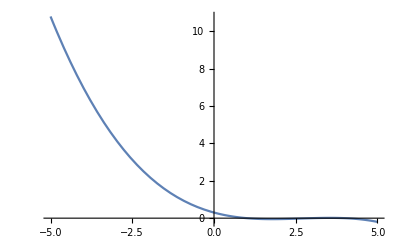

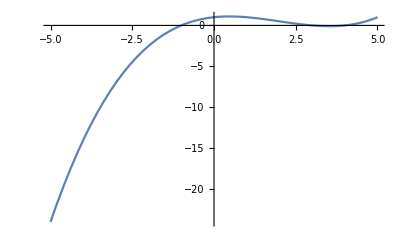

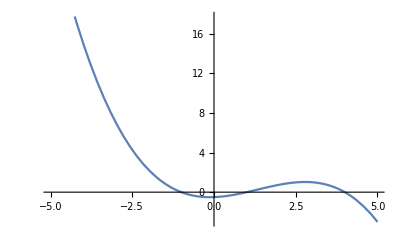

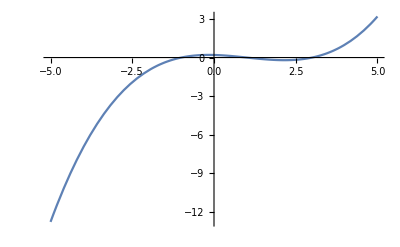

```mathematica
Clear[l0];
Clear[l1];
Clear[l2];
Clear[l3];
Clear[g0];
Clear[g1];
Clear[g2];
Clear[g3];

(* The four functions required in the Lagrange interpolation procedure *)
l0[x_] = ((x-1)(x-3)(x-4))/((-1-1)(-1-3)(-1-4));
l1[x_] = ((x+1)(x-3)(x-4))/((1 +1)(1-3)(1-4));
l2[x_] = ((x+1)(x-1)(x-4))/((3+1)(3-1)(3-4));
l3[x_] = ((x+1)(x-1)(x-3))/((4+1)(4-1)(4-3));

(* Plots of each *)
g0 = Plot[l0[x], {x, -5, 5}]
g1 = Plot[l1[x], {x, -5, 5}]
g2 = Plot[l2[x], {x, -5, 5}]
g3 = Plot[l3[x], {x, -5, 5}]
```

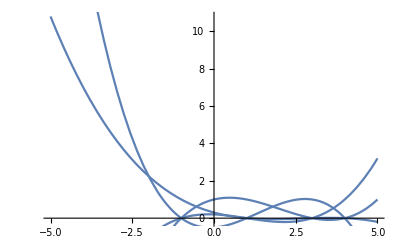

```mathematica
(* All plots layered on top of each other *)
Show[g0, g1, g2, g3]
```

## 4.1 # 4

Verify that the polynomials

		p(x) = 5 x^3 - 27 x^2 + 45x -21         q(x) = x^4 - 5 x^3 + 8 x^2 -5x + 3

interpolate the data

					x | 1 | 2 | 3 | 4
y | 2 | 1 | 6 | 47
					
and explain why this does not violate the uniqueness part of the theorem on existence of polynomial interpolation.

We can verify that the polynomials interpolate the given data by simply plugging in x inputs and checking if the y output matches what we expect.

```mathematica
Clear[p];
Clear[q];
p[x_] = 5x^3 - 27x^2 + 45x - 21;
q[x_] = x^4 - 5x^3 + 8x^2 - 5x+ 3;
q[1]
q[2]
q[3]
q[4]
p[1]
p[2]
p[3]
p[4]
```

2

1

6

47

2

1

6

47

Okay, now we can see that both our given functions definitely interpolate the given data. The reason that these functions don’t violate the uniqueness part of the theorem is because p and q are fundamentally different functions. They may have the same output, but no amount of manipulation of p(x) will yield an equation matching q(x) and vice-versa. This is due primarily to the fact that q(x) is of a higher degree than p(x), and no amount of manipulation can make a polynomial of degree 3 into a polynomial of degree 4 without multiplying by an extra x somewhere. So in this way, both p and q remain unique, despite have identical outputs. This means it is likely that both interpolating polynomials were generated using different methods, or possibly generated using a different ordering of points.

## 4.1 # 9

Given the data

				x | 0 | 1 | 2 | 4 | 6
f(x) | 1 | 9 | 23 | 93 | 259
				
do the following.

	a. Construct the divided-difference table.
		I find it easier to just create the table by hand over trying to use the Table command to do it for me.

```mathematica
Clear[f];
Clear [g];
Clear[q];
Clear[r];
Clear[pointArray];

pointArray = {{0,1},{1, 9}, {2, 23}, {4, 93}, {6, 259}};
p[x_] = InterpolatingPolynomial[pointArray, x];

f[x_, y_] = (p[y] - p[x]) / (y-x);
g[x_, y_, w_] = (f[y, w] - f[x, y])/ (w-x); 
q[x_, y_, w_, z_] = (g[y, w, z] - g[x, y, w]) / (z - x);
r[x_, y_, w_, z_, m_] = (q[y, w, z, m] - q[x, y, w, z]) / (m - x);
```

Now we have a collection of functions that we can use to find the individual terms of our divided difference table. 

For our x_i column our values are x = 0, 1, 2, 4, 6 and for our f_i column we have f = 1, 9, 23, 93, 259.

Lets calculate the four terms that will be in our f(x_i, x_j) column:

```mathematica
f[0, 1]
f[1, 2]
f[2, 4]
f[4, 6]
```

8

14

35

83

Now the three terms that will be in the f(x_i, x_j, x_l) column:

```mathematica
g[0, 1, 2]
g[1, 2, 4]
g[2, 4, 6]
```

3

7

12

Now the 2 terms in the f(x_i, x_j, x_l, x_m) column:

```mathematica
q[0, 1, 2, 4]
q[1, 2, 4, 6]
```

1

1

And finally the single term in the f(x_i, x_j, x_l, x_m, x_n) column:

```mathematica
r[0, 1, 2, 4, 6]
```

0

So now we can construct the divided difference table:

x | f | f(x_i, x_j) | f(x_i,x_j,x_l) | f(x_i,x_j,x_l,x_m) | f(x_i,x_j,x_l,x_m,x_n)
0 | 1 |   |   |   |  
1 | 9 | 8 |   |   |  
2 | 23 | 14 | 3 |   |  
4 | 93 | 35 | 7 | 1 |  
6 | 259 | 83 | 12 | 1 | 0

b. Using Newton’s interpolation polynomial, find an approximation to f(4.2)

```mathematica
(* I demonstrated at the end of problem 1 that using the InterpolatingPolynomial command will ouput an interpolating polynomial in nested Newton form, so I will be using that to calculate this polynomial. *)

Clear[pointArray];
pointArray = {{0,1}, {1, 9}, {2, 23}, {4, 93}, {6, 259}};
Clear[p];
p[x_] = InterpolatingPolynomial[pointArray, x];
p[4.2]
```

104.488

## 4.1 # 11

From census data, the approximate population of the United States was 150.7 million in 1950, 179.3 million in 1960, 203.3 million in 1970, 226.5 million in 1980, and 249.6 million in 1990. Using Newton’s interpolation polynomial for these data, find an approximate value for the population in 2000. Then use the polynomial to estimate the population in 1920 based on these data. What conclusion should be drawn?

```mathematica
censusData = {{1950, 150.7}, {1960, 179.3}, {1970, 203.3}, {1980, 226.5}, {1990, 249.6}};
Clear[p];
p[x_] = InterpolatingPolynomial[censusData, x]
```

249.6+(2.4725+(-0.007875+(0.000504167-0.0000129167 (-1960+x)) (-1970+x)) (-1950+x)) (-1990+x)

```mathematica
p[2000]
p[1920]
```

270.2

-47.2

So my understanding of this question is that we are intended to draw real-world conclusions from this data rather than more abstract conclusions about behavior of the polynomial. We obviously cannot have a population of -47.2 million in 1920, and at first I thought I had done something wrong when calculating my polynomial, but I then realized that it makes sense that certain x inputs have the occasional negative output because this is a polynomial of degree 5. The fact that we got a negative value tells me that whenever we are using the interpolating polynomial to model real-life data we should not just discard nonsensical negative values, but instead calculate Abs[p[x]]. Furthermore, from this data set we can draw the conclusion that we in the United States really need to slow down on having children. In the 80 year span from 1920 to 2000 our population grew from 47.2 million to 270.2 million and that is a massive jump. We can also see that the population increases exponentially, as population jumps from decade to decade increase greatly.

## 4.1 # 15

It is suspected that the table

				x | -2 | -1 | 0 | 1 | 2 | 3
y | 1 | 4 | 11 | 16 | 13 | -4
				
comes from a cubic polynomial. How can this be tested? Explain.

```mathematica
Clear[pointArray];
pointArray = {{-2, 1}, {-1, 4}, {0, 11}, {1, 16}, {2, 13}, {3, -4}};
Clear[p];
p[x_] = InterpolatingPolynomial[pointArray, x]
```

1+(2+x) (3+(2-x) (1+x))

Now we can tell this is a cubic polynomial just by analyzing the Newton interpolating polynomial. We see the function has three instances of an x value that are all related multiplicatively (we have (2+x)(3+(2-x)(1+x) instead of something like (2+x) + (2+(2-x)(1+x) ), so if we ignore the constants, because they don’t contribute anything to the degree of the function, at the very most we could have x*-x*x = -x^3. We cannot possibly create a polynomial of degree 4 from a function containing only three instances of x that are related multiplicatively. We could take this and make it into a square function, but we will still be left with a remaining x that can be distributed into the function and increase the degree by 1, meaning that at its simplest form this polynomial is cubic.

## 4.1 # 19

Let f(x) = x^3 + 2 x^2 + x + 1. Find the polynomial of degree 4 that interpolates the values of f at x = -2, -1, 0, 1, 2. Find the polynomial of degree 2 that interpolates the values of f at x = -1, 0, 1.

```mathematica
Clear[f];
f[x_] = x^3 + 2x^2 +x + 1;
degTwoArray = {{-1, f[-1]}, {0, f[0]}, {1, f[1]}};
InterpolatingPolynomial[degTwoArray, x]
```

1+2 x (1+x)

If we distribute the 2x, we create the polynomial p(x) = 1 + 2x + 2 x^2, which is our polynomial of degree 2 that interpolates the values of f at x = -1, 0, 1.

I spent a lot of time trying to figure out the next part, mainly because it took me a long time to find a range for my iterator that generated the values I needed to create a polynomial of degree 4. My solution is the opposite of graceful, it is very ugly and brute-force-y, but in the end I managed to generate a degree 4 polynomial. I included all of my attempts to show my thought process, but the solution is at the very bottom of the problem.

```mathematica
Clear[degFourTable];
degFourTable = Table[{.4i, f[.4i]}, {i, -5, 5}];
MatrixForm[degFourTable]
```

(-2. | -1.
-1.6 | 0.424
-1.2 | 0.952
-0.8 | 0.968
-0.4 | 0.856
0. | 1.
0.4 | 1.784
0.8 | 3.592
1.2 | 6.808
1.6 | 11.816
2. | 19.)

```mathematica
InterpolatingPolynomial[degFourTable, x]
```

-1.+(2.+x) (5.+(-2.+x) (2.+(0.+x) (1.+(1.2+x) (0.+(-1.2+x) (3.08395×10^-16+(1.6+x) (1.4456×10^-16+(-1.6+x) (-1.00389×10^-16+(0.4+x) (4.05381×10^-16+(-0.8+x) (5.07921×10^-17-7.11463×10^-16 (0.8+x))))))))))

From this attempt I got something with way too high of a degree, so I thought I could adjust my table and try again. I changed my iterator range to [-4, 4] hoping to get a smaller table. Of course, this also meant I needed to adjust how the table creates values to keep everything matching.

```mathematica
Clear[degFourTable];
degFourTable = Table[{.5i, f[.5i]}, {i, -4, 4}];
MatrixForm[degFourTable]
```

(-2. | -1.
-1.5 | 0.625
-1. | 1.
-0.5 | 0.875
0. | 1.
0.5 | 2.125
1. | 5.
1.5 | 10.375
2. | 19.)

```mathematica
InterpolatingPolynomial[degFourTable, x]
```

-1.+(2.+x) (5.+(-2.+x) (2.+1. (0.+x)))

Unfortunately, this is now back to being a degree 3 polynomial. So if my iterator range is [-5, 5] I get a polynomial that is way too large, and if my iterator range is [-4, 4] I get a polynomial that is too small. So maybe now I try iterating from [-3, 3], but that is going to damage the accuracy of my polynomial because I cannot multiply 3 by any value to create 2 to exact decimal places, at best I will get something like 1.9998.

```mathematica
Clear[degFourTable];
degFourTable = Table[{0.666i, f[0.666i]}, {i, -3, 3}];
MatrixForm[degFourTable]
```

(-1.998 | -0.990016
-1.332 | 0.853182
-0.666 | 0.925704
0. | 1.
0.666 | 2.84852
1.332 | 8.24371
1.998 | 18.958)

```mathematica
InterpolatingPolynomial[degFourTable, x]
```

-0.990016+(1.998+x) (4.992+(-1.998+x) (2.+(0.+x) (1.+(1.332+x) (2.3338×10^-16+(-1.332+x) (-1.7521×10^-16+2.53683×10^-16 (0.666+x))))))

Okay, so now we have something of degree 6. I can’t go to [-2, 2] because then I will just get the output from the function which I already know generates a polynomial of degree 3. I also can’t go down to [-1, 1] because then we have too few values to generate a polynomial of degree 4. I can, however, go down to something like [-2.5, 2.5].

```mathematica
Clear[degFourTable];
degFourTable = Table[{0.8i, f[0.8i]}, {i, -2.5, 2.5}];
MatrixForm[degFourTable]
```

(-2. | -1.
-1.2 | 0.952
-0.4 | 0.856
0.4 | 1.784
1.2 | 6.808
2. | 19.)

```mathematica
InterpolatingPolynomial[degFourTable, x]
```

-1.+(2.+x) (5.+(-2.+x) (1.6+(0.4+x) (1.+(-1.2+x) (-4.16334×10^-16+2.31296×10^-16 (1.2+x)))))

This is extremely  close, we now have a degree 5 polynomial. From here Im going to change my iterator by -0.1 until I finally generate my polynomial.

```mathematica
Clear[degFourTable];
degFourTable = Table[{0.83333333333i, f[0.83333333333i]}, {i, -2.4, 2.4}];
MatrixForm[degFourTable]
```

(-2. | -1.
-1.16667 | 0.967593
-0.333333 | 0.851852
0.5 | 2.125
1.33333 | 8.25926)

```mathematica
InterpolatingPolynomial[degFourTable, x]
```

-1.+(2.+x) (2.77778+(-1.33333+x) (1.+(1.+2.66454×10^-16 (-0.5+x)) (0.333333+x)))

Thankfully, the first value I attempted after [-2.5, 2.5] has worked. Our degree 4 polynomial is above.

## 4.1 # 23

Form a divided-difference table for the following and explain what happened.

						x | 1 | 2 | 3 | 1
y | 3 | 5 | 5 | 7
						
I immediately notice something strange with this table, we have f(1) = 3 and 7, which we know is just not possible, you can’t get two different outputs from the same input in the same function. This tells me that whatever is about to go wrong in this function is going to be related to this. 

I can’t solve this using my previous method where I created an interpolating polynomial and passed in to the calculations for f(x_i, x_j) because you simply cannot generate an interpolating polynomial with indistinct terms. Thus, I’m going to have to do the calculations by hand.

f(1, 2) = (5 - 3)/(2-1) = 2
f(2, 3) = (5 - 5) / (3 - 2) = 0
f(3, 1) = (7 - 5) / (1 - 3) = -1
g(1, 2, 3) = 0 - 2 / 3 - 1 = -1
g(2, 3, 1)= -1 - 0 / 1 - 2 =  1
q[1, 2, 3, 1] = 1 + 1 / 1 - 1 = 2 / 0

Now we have to stop because we got the biggest red flag in all of math: division by zero. This means we cannot generate a divided difference table for these values, which makes sense given that you wouldn’t be able to generate an interpolating polynomial from this data. We see that this is why interpolating polynomials require unique inputs, without unique inputs then one of the coefficients of the resulting interpolating polynomial will be an value divided by zero, which causes the whole process to crash.

## 4.1 # 31

Use the uniqueness of the interpolating polynomial to verify this summation (in the textbook).

I’m not really sure how to use the uniqueness to verify this, all my attempts have involved me trying to manipulate the summation in order to produce the same equation on both sides. I don’t feel like I solved this correctly, but I just can’t see how the uniqueness of the interpolation polynomial establishes this summation. Below is the work I did to manually demonstrate that the two sides of the summation are equivalent.

We know that the f [x_0, ..., x_n] term is equivalent to a_i, so that can be used to simplify this equation:

(Σ^n)_(i = 0) f(x_i) l_i(x) = (Σ_(i = 0))^n a_i (Π^(i - 1))_(j = 0) (x - x_j)

And now we can see that on the right hand side we have created the summation for of the Newton interpolation polynomial, so we can further simplify:

(Σ^n)_(i = 0) f(x_i) l_i(x) = p_n(x)

And now we have established the Lagrange form of the interpolation polynomial. In essence, the provided summation just establishes that the Newton form of the interpolation polynomial is equivalent to the Lagrange form of the interpolation polynomial, as we have demonstrated by simplifying the right hand side of the equation until we produced the Lagrange interpolation polynomial.

## 4.1 # 32

(Continuation) Show that the following explicit formula is valid for divided differences. 


(1) f(x_n) = (Σ_(i = 0))^n a_i (Π^(i - 1))_(j = 0) (x_n - x_j)

(2) a_n =  (Σ_(i = 0))^n f(x_i) (Π^n)_(j = 0) (x_n - x_j )^-1

Just by looking at these, my math experience tells me that they encode inverse equations, meaning that if n =1:

f (x_1) = a_0 + a_1 (x_1 - x_0) 

is generated by the first summation, and

a_1 = (f(x_1) - a_0)/(x_1 - x_0)= (f(x_1) - f(x_0))/(x_1 - x_0)

is generated by equation (2), with a_0 = f(x_0) (this equality is known to be factual when calculating divided difference terms).

Now what we may notice is that the a_1 term is actually calculating for one of the divided differences, namely the first f(x_i, x_j) term of the divided difference. This leads me to believe that further terms calculate further divided difference terms, but that still needs to be demonstrated. At this point, all we know is that when n = 1 we can use equation (2) to generate the first of the divided difference terms.

I was going to go further with this equation but I just realized it is 11:52 pm, so unfortunately I have to submit without finishing this problem. Hopefully I was on the right track.